18018699
1)

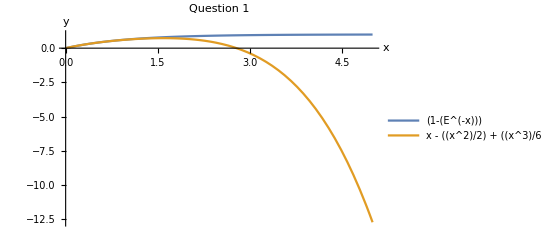

```mathematica
q1eqn1 = (1-(E^(-x)));
q1eqn2 = x - ((x^2)/2) + ((x^3)/6) - ((x^4)/24);
Plot[{q1eqn1,q1eqn2},{x,0,5},PlotRange->All,PlotLegends->{"(1-(E^(-x)))","x - ((x^2)/2) + ((x^3)/6) - ((x^4)/24)"}, AxesLabel-> {"x","y"}, PlotLabel->"Question 1"]
```

2)

```mathematica
q2eqn1 = a (x^3) + b (x^2) + c (x) + d == 0;
q2solutions = Solve[q2eqn1, x]
q2s1 = Replace[x,Part[q2solutions, 1]];
q2s2 = Replace[x,Part[q2solutions, 2]];
q2s3 = Replace[x,Part[q2solutions, 3]];
q2exp1 = Simplify[a (x^3) + b (x^2) + c (x) + d ];
q2exp2 = Simplify[a (x - q2s1) (x - q2s2) (x - q2s3)];
q2exp1 == q2exp2
```

{{x→-b/(3 a)-(2^(1/3) (-b^2+3 a c))/(3 a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))+((-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(3 2^(1/3) a)},{x→-b/(3 a)+((1+ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-((1-ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(6 2^(1/3) a)},{x→-b/(3 a)+((1-ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-((1+ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(6 2^(1/3) a)}}

True

```mathematica
q2replace1 = {a->5, b-> 4,c->3,d->0};
Solve[Replace[q2eqn1,q2replace1]]
```

{{x→0},{x→1/5 (-2-ⅈ √11)},{x→1/5 (-2+ⅈ √11)}}

3)
a)

```mathematica
q3list1 = PolyhedronData["Archimedean"];
q3solution1 = Sort[Table[{PolyhedronData[Part[q3list1, i],"VertexCount"],Part[q3list1, i]},{i,Length[q3list1]}]]//MatrixForm
```

(12 | Cuboctahedron
12 | TruncatedTetrahedron
24 | SmallRhombicuboctahedron
24 | SnubCube
24 | TruncatedCube
24 | TruncatedOctahedron
30 | Icosidodecahedron
48 | GreatRhombicuboctahedron
60 | SmallRhombicosidodecahedron
60 | SnubDodecahedron
60 | TruncatedDodecahedron
60 | TruncatedIcosahedron
120 | GreatRhombicosidodecahedron)

b)

```mathematica
q3solution2 =
```

4)
a)

```mathematica
Clear[a,b,c,d]
```

```mathematica
Clear[x];
q4diffeqn1 = (2 (y'[x]) (y'''[x]))-(3((y''[x])^2)) == 0;
q4aconditions1 = {y[1] == 1, y'[1]== -1, y''[1]== 2};
q4asolution = DSolve[{q4diffeqn1, q4aconditions1}, y[x],x]
```

{{y[x]→1/x}}

b)

```mathematica
q4bfunction1 = Replace[y[x], q4asolution];
q4bsolution1 = Limit[q4function1,x-> 0]
```

{Indeterminate}

c)

```mathematica
q4diffeqnSolution1 = (((a x) + b)/((c x) + d))
```

(b+a x)/(d+c x)

4) (2015)

```mathematica
q42diffeqn = D[u[x,t],t] - D[u[x,t],{x,2}] + (u[x,t] (D[u[x,t],x])) + (u[x,t]((1 - u[x,t])^2)) == 0;
q42solution = DSolve[q42diffeqn,u,{x,t}];
q42solution1 = q42solution[[1]]/.C[3]-> 0
Plot3D[u[x,t]/.q42solution1,{x,0,20},{t,0,20},PlotRange->All]
```

DSolve::nlpde: Solution requested to nonlinear partial differential equation. Trying to build a special solution.

{u→Function[{x,t},1/2 (1-Tanh[(3 t)/8-x/4-0])]}

-Graphics3D-

5)

```mathematica
q5B = {{-5,-8,0},{3,5,0},{1,2,-1}}
q5C = {{5,-3,2},{15,-9,6},{10,-6,4}}
q5D = {{2,3,-4},{0,1,0},{1/2,3/2,-1}}
```

{{-5,-8,0},{3,5,0},{1,2,-1}}

{{5,-3,2},{15,-9,6},{10,-6,4}}

{{2,3,-4},{0,1,0},{1/2,3/2,-1}}

```mathematica
q5B.q5B//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Matrix B is unipotent

```mathematica
q5C.q5C//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

Matrix C is nilpotent

```mathematica
q5D.q5D//MatrixForm
```

(2 | 3 | -4
0 | 1 | 0
1/2 | 3/2 | -1)

Matrix D is idempotent

6)
a)

7)
a)

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t]}}

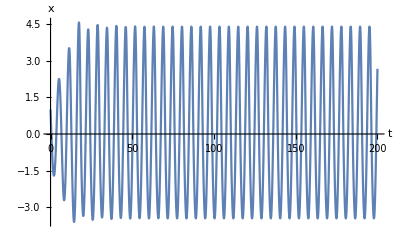

```mathematica
q7diffeqns = {D[x[t],t] + y[t] + z[t]==0, D[y[t],t] - ((a y[t]) + x[t])==0,D[z[t],t] - (b + (x[t] z[t]) - (c z[t]))==0};
q7aconditions = {x[0]== 1,y[0]== 1,z[0]== 1,a== 0.2,b== 0.2,c== 2.3};
q7asolution = NDSolve[{q7diffeqns,q7aconditions},{x[t],y[t],z[t]},{t,0,200}]
Plot[Evaluate[x[t]/.q7asolution],{t,0,200},AxesLabel->{"t","x"}]
```

b)

```mathematica
Plot3D[{Evaluate[x[t]/.q7asolution],Evaluate[y[t]/.q7asolution]},{t,100,200},PlotRange->Full]
```

Plot3D::argrx: Plot3D called with 2 arguments; 3 arguments are expected.

```mathematica
ParametricPlot3D[{Evaluate[x[t]/.q7asolution],Evaluate[y[t]/.q7asolution],Evaluate[z[t]/.q7asolution]},{t,100,200},PlotRange->Full]
```

-Graphics3D-

c)